Si può automatizzare la ricerca della biforcazione. Per determinare la biforcazione n-esima, si parte da un appropriato valore di μ inferiore a quello di biforcazione (stimato ad occhio) e si confrontano, per un N opportunamente grande, le iterate N-esima e (N+2^n)-esima di uno stesso punto inziale. Se sono molto vicini, non siamo ancora alla biforcazione, e bisogna aumentare μ. Appena cominciano ad allontanarsi, siamo arrivati alla biforcazione.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x(1-x)
fn[μ_,x_,n_]:=Nest[f[μ,#]&,x,n]
dist[μ_,x0_,Ν_,n_]:=Abs[fn[μ,x0,Ν]-fn[μ,x0,Ν+2^n]]
indagine[n_,x0_,{min_,max_,step_}]:=ParallelTable[{μ,dist[μ,x0,10^4,n]},{μ,min,max,step}]
```

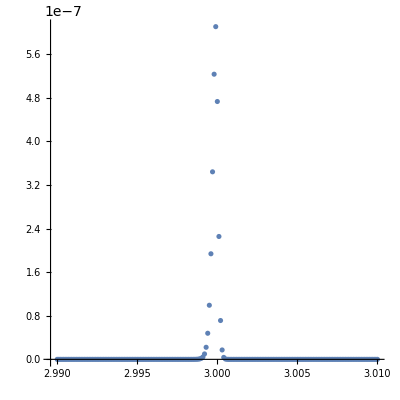

```mathematica
ListPlot[indagine[2,0.4,{2.99,3.01,10^-4}],AspectRatio->1,PlotRange->Full]
```

```mathematica
Module[
{
ind=indagine[2,0.4,{2.99,3.01,10^-3}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

{{3.,4.72951×10^-7}}

```mathematica
Module[
{
ind=indagine[3,0.3,{3.4494,3.45,10^-6}],
val,
spike
},
val=Last/@ind;
spike=Max@val;
Cases[ind,{_,spike}]
]
```

{{3.44945,6.21788×10^-7}}

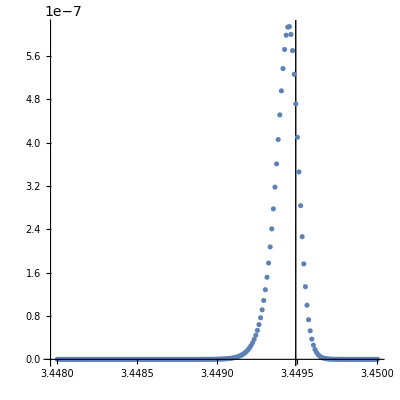

```mathematica
ListPlot[indagine[3,0.4,{3.448,3.45,10^-5}],AspectRatio->1,PlotRange->Full,Epilog->{InfiniteLine[{{1+√6,0},{1+√6,1}}]}]
```

```mathematica
(1+√6-3.4494459999999996)/(1+√6)
```

0.0000126809

Quindi non solo il metodo pare funzionare, ma gli errori numerici che compie possono essere inferiori all’1%! Godo.